# Fourier Transformation. Starter Code.

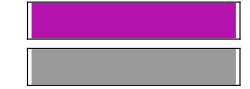

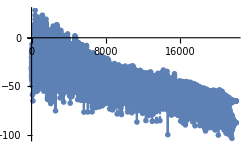

```mathematica
ClearAll["Global`*"]
record1 = Sound[SoundNote["G",1,"Violin"]]
Periodogram[record1]
```

#### Shifting sound by a fixed frequency

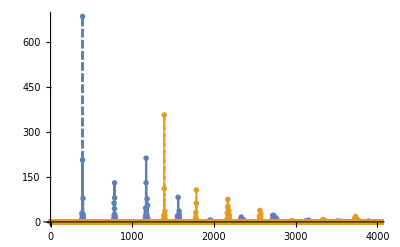

```mathematica
res=AudioFrequencyShift[record1,Quantity[1000,"Hertz"]]

Periodogram[{record1,res},PlotRange->{{0,4000},All},ScalingFunctions->"Absolute"]
```

#### Shifting sound using a given coefficient

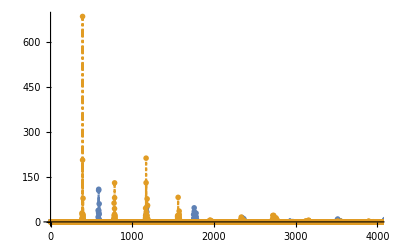

```mathematica
new = AudioPitchShift[record1, 1.5]
Periodogram[{new, record1},PlotRange->{{0,4000},All},ScalingFunctions->"Absolute"]
```

#### Working with data

```mathematica
(* get Amplitude data in time domain *)
AudioData[new]
AudioData[new][[1]];
AudioData[new][[2]];
ListPlot[AudioData[new][[1]]];
ListPlot[AudioData[new][[2]]];
```

{{1.00987×10^-8,6.48649×10^-8,1.72839×10^-7,6.97719×10^-7,1.1602×10^-6,-7.36842×10^-7,-7.37031×10^-6,-0.0000168434,-0.0000248575,-0.0000275612,-0.0000268305,45547,0.0354259,0.0278062,0.023525,0.0199708,0.016173,0.0161686,0.0179116,0.020459,0.0192367,0.012088},1}
 |  |  |  |

{{2.89219×10^-9,0.0000370022,0.000237798,0.000433334,0.000134153,0.000097621,0.00010709,0.000049158,0.000230403,0.000475326,45548,0.000208603,0.000475326,0.000230403,0.000049158,0.00010709,0.000097621,0.000134153,0.000433334,0.000237798,0.0000370022},{1}}
 |  |  |  |

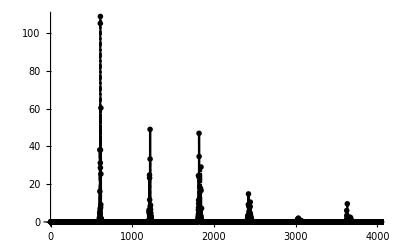

```mathematica
(* squared magnitude of the discrete Fourier transform (power spectrum) of list. *)
PerData = PeriodogramArray[new]
ListLinePlot[PerData,PlotRange->{{0, 4000}, All}]
```

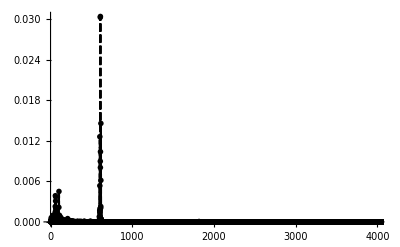

```mathematica
(* apply filter if needed *)
newFiltered =BandpassFilter[new, {400, 1000}]
PerDataFiltered = PeriodogramArray[newFiltered];
ListLinePlot[PerDataFiltered,PlotRange->{{0, 4000}, All}]
```